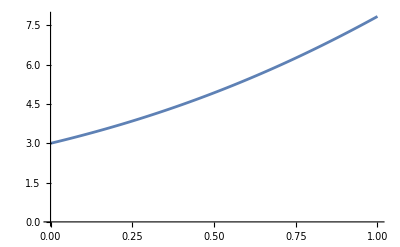

```mathematica
data = {{0,3},{0.01,3.03015},{0.02,3.0606},{0.03,3.09136},{0.04,3.12243},{0.05,3.15381},{0.06,3.1855},{0.07,3.21751},{0.08,3.24985},{0.09,3.2825},{0.1,3.31548},{0.11,3.34879},{0.12,3.38243},{0.13,3.4164},{0.14,3.45071},{0.15,3.48536},{0.16,3.52035},{0.17,3.55569},{0.18,3.59137},{0.19,3.6274},{0.2,3.66378},{0.21,3.70051},{0.22,3.7376},{0.23,3.77505},{0.24,3.81286},{0.25,3.85103},{0.26,3.88957},{0.27,3.92847},{0.28,3.96774},{0.29,4.00739},{0.3,4.0474},{0.31,4.08779},{0.32,4.12856},{0.33,4.16971},{0.34,4.21124},{0.35,4.25315},{0.36,4.29544},{0.37,4.33812},{0.38,4.38119},{0.39,4.42464},{0.4,4.46849},{0.41,4.51273},{0.42,4.55737},{0.43,4.6024},{0.44,4.64782},{0.45,4.69365},{0.46,4.73987},{0.47,4.7865},{0.48,4.83353},{0.49,4.88096},{0.5,4.92879},{0.51,4.97703},{0.52,5.02568},{0.53,5.07473},{0.54,5.12419},{0.55,5.17406},{0.56,5.22434},{0.57,5.27504},{0.58,5.32614},{0.59,5.37765},{0.6,5.42958},{0.61,5.48192},{0.62,5.53468},{0.63,5.58785},{0.64,5.64143},{0.65,5.69543},{0.66,5.74985},{0.67,5.80468},{0.68,5.85992},{0.69,5.91559},{0.7,5.97166},{0.71,6.02816},{0.72,6.08507},{0.73,6.14239},{0.74,6.20013},{0.75,6.25829},{0.76,6.31686},{0.77,6.37584},{0.78,6.43524},{0.79,6.49505},{0.8,6.55528},{0.81,6.61592},{0.82,6.67697},{0.83,6.73843},{0.84,6.8003},{0.85,6.86258},{0.86,6.92526},{0.87,6.98836},{0.88,7.05186},{0.89,7.11576},{0.9,7.18007},{0.91,7.24478},{0.92,7.30989},{0.93,7.3754},{0.94,7.44131},{0.95,7.50762},{0.96,7.57431},{0.97,7.6414},{0.98,7.70889},{0.99,7.77676},{1,7.84501}};
ListPlot[data, Joined->True]
```

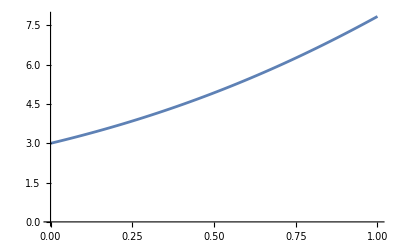

```mathematica
sol = DSolve[{y'[x]==y[x]-x^3, y[0]==3}, y[x], x];
Plot[Evaluate[y[x]/.sol], {x, 0, 1}, AxesOrigin->{0,0}]
```

```mathematica
table=Table[{x,y[x]/. sol/. {val_}:>val},{x,0,1,0.01}];
Grid[table]
```

0. | 3.
0.01 | 3.03015
0.02 | 3.0606
0.03 | 3.09136
0.04 | 3.12243
0.05 | 3.15381
0.06 | 3.18551
0.07 | 3.21752
0.08 | 3.24985
0.09 | 3.28251
0.1 | 3.31549
0.11 | 3.3488
0.12 | 3.38244
0.13 | 3.41641
0.14 | 3.45072
0.15 | 3.48537
0.16 | 3.52036
0.17 | 3.5557
0.18 | 3.59138
0.19 | 3.62741
0.2 | 3.66379
0.21 | 3.70053
0.22 | 3.73762
0.23 | 3.77507
0.24 | 3.81288
0.25 | 3.85105
0.26 | 3.88959
0.27 | 3.92849
0.28 | 3.96776
0.29 | 4.00741
0.3 | 4.04742
0.31 | 4.08782
0.32 | 4.12858
0.33 | 4.16973
0.34 | 4.21126
0.35 | 4.25317
0.36 | 4.29547
0.37 | 4.33815
0.38 | 4.38122
0.39 | 4.42468
0.4 | 4.46853
0.41 | 4.51277
0.42 | 4.5574
0.43 | 4.60243
0.44 | 4.64786
0.45 | 4.69369
0.46 | 4.73991
0.47 | 4.78654
0.48 | 4.83357
0.49 | 4.881
0.5 | 4.92884
0.51 | 4.97708
0.52 | 5.02573
0.53 | 5.07478
0.54 | 5.12424
0.55 | 5.17412
0.56 | 5.2244
0.57 | 5.27509
0.58 | 5.3262
0.59 | 5.37771
0.6 | 5.42964
0.61 | 5.48199
0.62 | 5.53474
0.63 | 5.58792
0.64 | 5.6415
0.65 | 5.6955
0.66 | 5.74992
0.67 | 5.80475
0.68 | 5.86
0.69 | 5.91566
0.7 | 5.97174
0.71 | 6.02824
0.72 | 6.08515
0.73 | 6.14248
0.74 | 6.20022
0.75 | 6.25837
0.76 | 6.31695
0.77 | 6.37593
0.78 | 6.43534
0.79 | 6.49515
0.8 | 6.55538
0.81 | 6.61602
0.82 | 6.67707
0.83 | 6.73853
0.84 | 6.8004
0.85 | 6.86268
0.86 | 6.92537
0.87 | 6.98847
0.88 | 7.05197
0.89 | 7.11588
0.9 | 7.18019
0.91 | 7.2449
0.92 | 7.31002
0.93 | 7.37553
0.94 | 7.44144
0.95 | 7.50775
0.96 | 7.57445
0.97 | 7.64154
0.98 | 7.70902
0.99 | 7.7769
1. | 7.84515